```mathematica
SetDirectory[NotebookDirectory[]];

Needs["PlotLegends`"]
(*Names (Labels)*)
labels = {Rotate["STPA",90 Degree],Rotate["R^ST",90 Degree],Rotate["Med",90 Degree],Rotate["Seq",90 Degree]};
chartStyles = {
Directive[Black]
,
Directive[GrayLevel[0.6]]
,
Directive[Black,Dashed,EdgeForm[Thin]]
,
Directive[GrayLevel[0.6],Dotted]
};
lineStyles = {
Directive[Black]
, 
Directive[GrayLevel[0.6]]
,
Directive[Black,Dashed]
,
Directive[GrayLevel[0.6],Dotted]
};
pointStyles={Triangle[],Circle[],Triangle[],Circle[]};
plotStyles={Black
,
GrayLevel[0.4] };
(* create chart Legend *)
chartLegend =Table[{Graphics[
{chartStyles[[i]],
Rectangle[{0,0},{25.0,4}]
}
],
labels[[i]]
},{i,1,Length[labels]}];
Legend[chartLegend,LegendShadow->False,LegendSize->{2,1.5},LegendOrientation->Horizontal]//InputForm
chartLegend = Graphics[%]

(* create line Legend *)
lineLegend =Table[{Graphics[
{lineStyles[[i]],
EdgeForm[Thick],
Line[{{0,0},{25.0,0}}]
}
],labels[[i]]
},{i,1,Length[labels]}];
Legend[
lineLegend,
LegendShadow->False,
LegendSize->{Length[labels],1.5},
LegendOrientation->Horizontal,
LegendSpacing->Tiny]//InputForm
lineLegend = Graphics[%]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

-Graphics-

-Graphics-

GraphicsGroup[{GrayLevel[0], Rectangle[{-1, -1}, {3, 0.5}], GrayLevel[1], EdgeForm[{Thickness[0.001], GrayLevel[0]}], Rectangle[{-1, -1}, {3, 0.5}], 
  Inset[Graphics[{{{Inset[Graphics[{Directive[GrayLevel[0]], EdgeForm[Thickness[Large]], Line[{{0, 0}, {25., 0}}]}], {0.08, 0.08}, {Left, Bottom}, {1, 1}], 
       Text[Rotate["STPA", 90*Degree], {0.58, 1.1600000000000001}, {0, -1}, {1, 0}]}, 
      {Inset[Graphics[{Directive[GrayLevel[0.6]], EdgeForm[Thickness[Large]], Line[{{0, 0}, {25., 0}}]}], {1.24, 0.08}, {Left, Bottom}, {1, 1}], 
       Text[Rotate["\!\(\*SuperscriptBox[\(R\), \(ST\)]\)", 90*Degree], {1.74, 1.1600000000000001}, {0, -1}, {1, 0}]}, 
      {Inset[Graphics[{Directive[GrayLevel[0], Dashing[{Small, Small}]], EdgeForm[Thickness[Large]], Line[{{0, 0}, {25., 0}}]}], {2.4, 0.08}, {Left, Bottom}, 
        {1, 1}], Text[Rotate["Med", 90*Degree], {2.9, 1.1600000000000001}, {0, -1}, {1, 0}]}, 
      {Inset[Graphics[{Directive[GrayLevel[0.6], Dashing[{0, Small}]], EdgeForm[Thickness[Large]], Line[{{0, 0}, {25., 0}}]}], {3.56, 0.08}, {Left, Bottom}, 
        {1, 1}], Text[Rotate["Seq", 90*Degree], {4.0600000000000005, 1.1600000000000001}, {0, -1}, {1, 0}]}}, {}}, AspectRatio -> 0.375, 
    PlotRange -> {{-0.1, 4.739999999999999}, {-0.1, 2.2600000000000002}}], {-1, -1}, {Left, Bottom}, {4, 1.5}]}]

```mathematica
extractData[data_,dim_,block_,buffer_,test_,incpos_,value_]:=
Module[{
l,
dl,
bl,
bul,
il,
dpos,
bpos,
bupos,
tpos,
pos
},
l = Length[data];
dl = Length[dims];
bl=Length[blockSizes];
bul=Length[bufferSizes];
il=Length[incSizes];
dpos=(dim-1)*l/dl;
bpos = (block-1)*l/(dl*bl);
bupos = (buffer-1)*l/(dl*bl*bul);
tpos = (test-1)*l/(dl*bl*bul*tests);
pos = dpos+bpos+bupos+tpos+incpos;
data[[pos]]
];
mergeTests[data_,dim_,block_,buffer_,incSize_,value_,scale_]:=Module[{},
Table[extractData[data,dim,block,buffer,test,incSize,value][[value]]/scale,{test,1,tests}]
];
(*read in evaluation setups*)

readInSetup[evaluationSetup_]:=Module[{},
xml =Import[evaluationSetup,"XML","IncludeNamespaces"->False];
evalFunction = Cases[xml,XMLElement["evalFunction",_,List[n_]]->n,Infinity][[1]];
bufferSizes = Cases[xml,XMLElement["bufferSize",_,List[n_]]->n,Infinity];
dims = Cases[xml,XMLElement["dim",_,List[n_]]->n,Infinity];
dims=Table[ImportString[dims[[d]],"List"][[1]],{d,1,Length[dims],1}];
blockSizes = Cases[xml,XMLElement["blockSize",_,List[n_]]->n,Infinity];
initialSize = Cases[xml,XMLElement["initialSize",_,List[n_]]->n,Infinity][[1]];
initialSize=ImportString[initialSize,"List"][[1]];
incSizes=Cases[xml,XMLElement["incSize",_,List[n_]]->n,Infinity];
incSizes=Table[ImportString[incSizes[[d]],"List"][[1]],{d,1,Length[incSizes],1}];
sizes = {initialSize+incSizes[[1]]*0.9};
For[i=1,i<Length[incSizes],i++,
AppendTo[sizes,sizes[[i]]+incSizes[[i+1]]*0.9]
];
(*TODO*)
sizes={10.9,20.8,30.7,40.6,50.5,60.4,70.3,80.2,90.1,100};
sizesString = {"\n10.9","\n20.8","\n30.7","\n40.6","\n50.5","\n60.4","\n70.3","\n80.2","\n90.1","\n100"};
queries= Cases[xml,XMLElement["queries",_,List[n_]]->n,Infinity][[1]];
queries=ImportString[queries,"List"][[1]];
tests =Cases[xml,XMLElement["tests",_,List[n_]]->n,Infinity][[1]];
tests=ImportString[tests,"List"][[1]];
]
```

```mathematica
ListBoxWhiskerNoLabel[dataSets_, value_,label_,dim_,scale_,maxy_]:=Module[{mydata},
mydata =MakeBoxWhiskerData[dataSets,value,dim,scale];
BoxWhiskerChart[mydata,"Mean",ChartStyle->chartStyles,Epilog->Inset[dims[[dim]]" dimensions",{3,maxy*0.8}],AspectRatio->0.4,ImageSize->{Length[dataSets]*300},ImagePadding->{{65,47},{5,5}},FrameLabel->{{None,label},{None,None}},BaseStyle->{FontFamily->"Time",FontSize->fontSize},PlotRange->{0,maxy}]
]
ListBoxWhisker[dataSets_, value_,label_,dim_,scale_,maxy_]:=Module[{mydata},
mydata =MakeBoxWhiskerData[dataSets,value,dim,scale];
BoxWhiskerChart[mydata,"Mean",ChartStyle->chartStyles,ChartLabels->{sizesString,labels},Epilog->Inset[dims[[dim]]" dimensions",{3,maxy.8}],AspectRatio->0.4,ImageSize->{Length[dataSets]*300},ImagePadding->{{65,47},{100,5}},FrameLabel->{{None,label},{"Number of elements (in thousands)",None}},BaseStyle->{FontFamily->"Time",FontSize->fontSize},PlotRange->{0,maxy}]
]
MakeBoxWhiskerData[dataSets_,value_,dim_,scale_]:=Module[{data},
data=Table[Import[dataSets[[i]],HeaderLines->2],{i,1,Length[dataSets]}];
Table[Table[mergeTests[data[[i]],dim,1,buffer,size,value,scale],{i,1,Length[data]}],{size,1,Length[sizes],1}]
]
```

```mathematica
MakeListLineData[dataSets_,value_,dim_,scale_]:=Module[{data},
data=Table[Import[dataSets[[i]],HeaderLines->2],{i,1,Length[dataSets]}];
Table[Table[{sizes[[size]],Mean[mergeTests[data[[i]],dim,1,buffer,size,value,scale]]},{size,1,Length[sizes],1}],{i,1,Length[data]}]
]

ListLine[dataSets_,value_,label_,dim_,scale_,maxy_]:=Module[{data},
data = MakeListLineData[dataSets,value,dim,scale];
ListLinePlot[data,PlotStyle->lineStyles,PlotMarkers->Automatic,PlotRange->{{9,Automatic},{0,maxy}},Epilog->Inset[dims[[dim]]" dimensions",{25,maxy*0.8}],BaseStyle->{FontFamily->"Time",FontSize->fontSize},AspectRatio->0.4,ImageSize->{600},Frame->True,FrameLabel->{{None,label},{"Number of elements (in thousands)",None}},FrameTicks->{{Automatic,Automatic},{sizes,Automatic}},ImagePadding->{{65,47},{50,10}}]

]
ListLineNoLabel[dataSets_,value_,label_,dim_,scale_,maxy_]:=Module[{data},
data = MakeListLineData[dataSets,value,dim,scale];
ListLinePlot[data,PlotStyle->lineStyles,PlotMarkers->Automatic,PlotRange->{{9,Automatic},{0,maxy}},Epilog->Inset[dims[[dim]]" dimensions",{25,maxy*0.8}],BaseStyle->{FontFamily->"Time",FontSize->fontSize},AspectRatio->0.4,ImageSize->{600},Frame->True,FrameLabel->{{None,label},{None,None}},FrameTicks->{{Automatic,Automatic},{None,Automatic}},ImagePadding->{{65,47},{10,10}}]

]
```

```mathematica
My3DPlotNorm[rtpData_, rstData_,value_,zaxislabel_,maxz_]:=Module[{},
data = Import[rtpData,"HeaderLines"->2];
table3d1=Flatten[Table[{sizes[[size]](*size*),(*dims[[dim]]/5*)dims[[dim]],Mean[mergeTests[data,dim,1,buffer,size,value,1]]
/Mean[mergeTests[data,1,1,buffer,1,value,1]]
},{size,1,Length[incSizes]},{dim,1,Length[dims]}],1];
data = Import[rstData,"HeaderLines"->2];
table3d2=Flatten[Table[{sizes[[size]](*size*),(*dims[[dim]]/5*)dims[[dim]],Mean[mergeTests[data,dim,1,buffer,size,value,1]]
/Mean[mergeTests[data,1,1,buffer,1,value,1]]
},{size,1,Length[incSizes]},{dim,1,Length[dims]}],1];
ListPlot3D[{table3d1,table3d2},PlotStyle->plotStyles,PlotLegends->None,PlotRange->{Full,Full,{0,maxz}},Mesh->{(*Length[incSizes]-2*)sizes,dims(*Table[dims[[dim]]/5,{dim,1,Length[dims]}]*)},ColorFunction->False,Lighting->"Neutral",AxesLabel->{"Number of\nelements (in thousands)","\nNumber of\ndimensions",Rotate["relative average "<>zaxislabel<>"\n",90 Degree]},
Ticks->{sizes(*Table[s,{s,1,Length[incSizes],1}]*),dims(*Table[dims[[dim]]/5,{dim,1,Length[dims]}]*)(*dims*),Automatic},ImageSize->{600},ImagePadding->{{65,47},{30,0}},BaseStyle->{FontFamily->"Time",FontSize->fontSize}
]
]
```

```mathematica
EvalSetQueries[setup_,dataSets_,label_,unit_,scale_ ,maxz_,maxy5_,maxy50_]:=Module[{box1,box2,box3,normPlot},
readInSetup[setup];

box1=ListBoxWhiskerNoLabel[dataSets,7,label<>" [" <>unit<>"]",1,queries*scale,maxy5];
box2=ListBoxWhisker[dataSets,7,label<>" [" <>unit<>"]",Length[dims],queries*scale,maxy50];
normPlot=My3DPlotNorm[dataSets[[1]],dataSets[[2]],7,label<>"[-]",maxz];

Column[{normPlot,box1,box2},Center]
]
EvalSetQueriesList[setup_,dataSets_,label_,unit_,scale_ ,maxz_,maxy5_,maxy50_]:=Module[{box1,box2,box3,normPlot},
readInSetup[setup];

box1=ListLineNoLabel[dataSets,7,label<>" [" <>unit<>"]",1,queries*scale,maxy5];
box2=ListLine[dataSets,7,label<>" [" <>unit<>"]",Length[dims],queries*scale,maxy50];
normPlot=My3DPlotNorm[dataSets[[1]],dataSets[[2]],7,label<>"[-]",maxz];

Column[{normPlot,box1,box2},Center]
]
EvalSetQueriesListH[setup_,dataSets_,label_,unit_,scale_ ,maxz_,maxy5_,maxy50_]:=Module[{box1,box2,box3,normPlot},
readInSetup[setup];

box1=ListLineNoLabel[dataSets,7,label<>" [" <>unit<>"]",1,queries*scale,maxy5];
box2=ListLine[dataSets,7,label<>" [" <>unit<>"]",Length[dims],queries*scale,maxy50];
normPlot=My3DPlotNorm[dataSets[[1]],dataSets[[2]],7,label<>"[-]",maxz];

Row[{normPlot,Column[{box1,box2}]}]
]
```

# Evaluation

```mathematica
(*buffer size (should be set to 1)*)
buffer = 1;
fontSize = 17;
basePath ="/Users/mmenning/Forschung/Index/documents/ojdb/pics";
```

Sequential Scan min and max

```mathematica
readInSetup["memClusterSetup.xml"]
N[Mean[mergeTests[Import["sequential/memClusterSequential.dat",HeaderLines->2],1,1,buffer,1,7,1000000000]]]
N[Mean[mergeTests[Import["sequential/memClusterSequential.dat",HeaderLines->2],7,1,buffer,10,7,1000000000]]]
```

1.12232

15.9875

```mathematica
readInSetup["memUniformSetup.xml"]
N[Mean[mergeTests[Import["sequential/memUniformSequential.dat",HeaderLines->2],1,1,buffer,1,7,1000000000]]]
N[Mean[mergeTests[Import["sequential/memUniformSequential.dat",HeaderLines->2],7,1,buffer,10,7,1000000000]]]
```

1.18002

15.9839

## On - Disk

Setup Uniform On - Disk

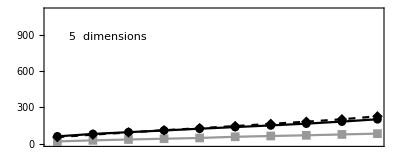
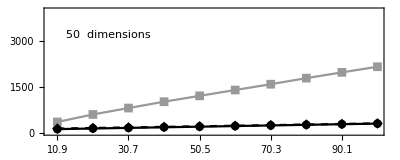
-Graphics3D-
-Graphics-
-Graphics-

```mathematica
graphs=EvalSetQueriesList["uniformSetupZeroBuf.xml",{"rtptree/uniformUnOptiZeroBuf.dat","rsttree/uniformZeroBuf.dat","rtptree/ioBadMedianUniform.dat"},"query cost","I/O",1,115,1100,4000]
Export[basePath<>"uniformOnDisk.png",graphs];
```

Setup Cluster On - Disk

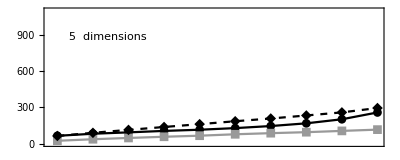
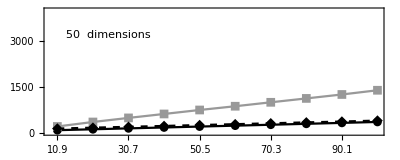
-Graphics3D-
-Graphics-
-Graphics-

```mathematica
graphs=EvalSetQueriesList["clusterSetupZeroBuf.xml", {"rtptree/clusterUnOptiZeroBuf.dat", "rsttree/clusterZeroBuf.dat","rtptree/ioBadMedianCluster.dat"}, "query cost", "I/O",1,115,1100,4000]
Export[basePath<>"clusterOnDisk.png",graphs];
```

Setup Skewed On - Disk

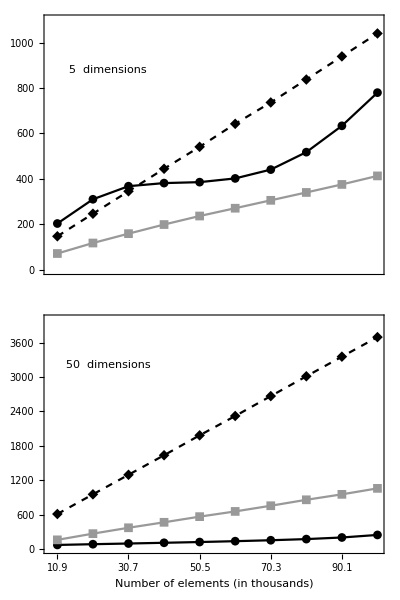
-Graphics3D--Graphics-

```mathematica
graphs=EvalSetQueriesListH["skewedSetupZeroBuf.xml", {"rtptree/ioSkewed.dat", "rsttree/ioSkewed.dat","rtptree/ioBadMedianSkewed.dat"}, "query cost", "I/O",1,100,1100,4000]
Export[basePath<>"skewedOnDisk.png",graphs];
```

## In - Memory

Setup Uniform In - Memory

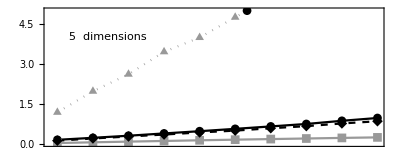
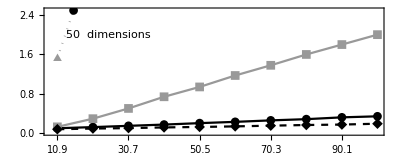
-Graphics3D-
-Graphics-
-Graphics-

```mathematica
graphs=EvalSetQueriesList["memUniformSetup.xml", {"rtptree/memUniformRTPTreeUnOpti.dat","rsttree/memUniformRSTTreeConstP.dat","rtptree/memBadMedianUniform.dat","sequential/memUniformSequential.dat"} ,"query cost", "ms",1000000,80,5,2.5]
Export[basePath<>"uniformInMemory.png",graphs];
```

Setup Cluster In - Memory

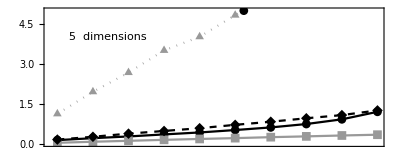
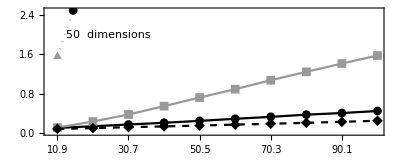
-Graphics3D-
-Graphics-
-Graphics-

```mathematica
graphs=EvalSetQueriesList["memClusterSetup.xml", {"rtptree/memClusterRTPTreeUnOpti.dat", "rsttree/memClusterRSTTreeConstP.dat","rtptree/memBadMedianCluster.dat","sequential/memClusterSequential.dat"}, "query cost", "ms",1000000,80,5,2.5]
Export[basePath<>"clusterInMemory.png",graphs];
```

Setup Skewed In - Memory

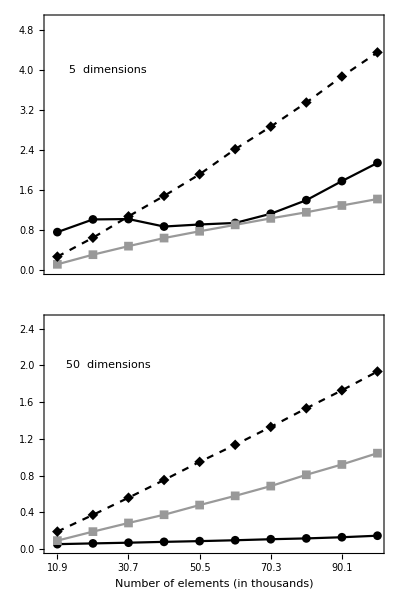
-Graphics3D--Graphics-

```mathematica
graphs=EvalSetQueriesListH["memSkewedSetup.xml", {"rtptree/memSkewed.dat", "rsttree/memSkewed.dat","rtptree/memBadMedianSkewed.dat","sequential/memSkewed.dat"}, "query cost", "ms",1000000,80,5,2.5]
Export[basePath<>"skewedInMemory.png",graphs];
```